# Wilberforce Pendulum modelling PHYS1201 ASE project, 2022

## By Campbell McTernan and Aditya Singh Tejas

## Introduction

This project requires the creation and investigation of a complex mechanical system as least as complex as a double pendulum. For this task, we have chosen the Wilberforce pendulum which was first described by the physicist Lionel Robert Wilberforce  in 1896. The Wilberforce pendulum is constructed by hanging  a mass which is free to rotate in the direction of the coils, with certain harmonic properties which allow for energy to alternate between purely vertical and rotational motion. This is achieved through a coupling of the rotational and spring potential energy of the system. 

This investigation focuses on the description and analysis of the pendulum, using the Euler-Lagrange equations of motion to predict the pendulum’s path, and representing this in Mathematica. This document primarily serves to describe the theoretical implications of design choices for the pendulum and to predict its path using computational software.

## The Wilberforce Pendulum

The mass  is free to slide along a frictionless rail. The Wilberforce pendulum consists of a cylindrical mass  (moment of inertia ) suspended by a helical spring of natural length , stretched length l + s(t), longitudinal spring constant  and torsional spring constant . We assume that the spring has negligible mass and is rigid along its axis throughout the experiment. The cylinder must hang such that its axis is always in the plane orthogonal to the direction of the spring, and is free to rotate along this plane. The spring makes an angle  from the vertical and the tracked point on the cylinder creates an angle  from the measured from the starting point in its rotational plane . The horizontal position of the mass  is noted as  from the origin  : see figure. We choose the reference of the gravitational potential energy to be zero at the height of mass . Note that the motion is actually in 3 dimensions but, the z-axis (into the page) is essential irrelevant for the motion of equations, as it can be represented by .


	-Graphics-


Note that there are four coordinates, that is, θ, ,  and . There are four Euler-Lagrange equations and these must be solved simultaneously.

### Deriving the Euler-Lagrange equations

Start by deriving the kinetic and potential energies, and hence the Lagrangian. Although you should formulate the dynamics using the angles, θ_1 and θ_2, it is easier to set it up in Cartesian coordinates:


We will start by considering all aspects of energy in the system to later conclude on the Lagrangian:

Kinetic energy
As the entire system is free to slide along a rail, the system can obtain velocity and thus kinetic energy. Defining  to be the velocity of the system, we thus have  . Furthermore, the cylinder  itself will have velocity relative to the system  and rotational energy dependant on the rotational velocity  given by  and  . 

Thus, the total kinetic energy of the system is  , so



Potential energy

We know that a spring with spring constant  and stretch length  has a spring potential  . We also know that the torsional potential of the spring is . Since these potentials are coupled, we furthermore have the potential  which represents the shared energy held during the transfer of energy between  and  in the system. As there are only two coupled components of potential, this relationship is linear and proportional to  and . Thus, assume  where  is some constant. Finally, as this Wilberforce experiment has been made unique by the inclusion of traditional swinging pendulum motion, we also have gravitational potential  . 

Thus, the total kinetic energy of the system is  , so



Lagrangian

```mathematica
Subscript[x, 0] = x[t]; Subscript[y, 0] = 0;
Subscript[x, 1]=(l+s[t]) Sin[ θ[t]]+ x[t];Subscript[y, 1]=-(l+s[t]) Cos[θ[t]];
Subscript[x, 2]=r Cos[α[t]] Cos[ θ[t]]+(l+s[t]) Sin[ θ[t]]+ x[t];Subscript[y, 2]=r Cos[α[t]] Sin[ θ[t]]+-(l+s[t]) Cos[θ[t]];
i = (M r^2)/3;
```

The kinetic energy is then:

```mathematica
K=0.5 (m+M) (D[Subscript[x, 0],t]^2)+0.5 M(D[Subscript[x, 1],t]^2+D[Subscript[y, 1],t]^2)+0.5 i ((D[α[t], t])^2)
```

0.151 x'[t]^2+0.000125 α'[t]^2+0.15 ((Sin[θ[t]] s'[t]+x'[t]+Cos[θ[t]] (0.3+s[t]) θ'[t])^2+(-Cos[θ[t]] s'[t]-(-0.3-s[t]) Sin[θ[t]] θ'[t])^2)

Use FullSimplify to simplify trigonometric terms.

```mathematica
K=FullSimplify[K]
```

0.151 x'[t]^2+0.000125 α'[t]^2+0.15 ((Sin[θ[t]] s'[t]+x'[t]+Cos[θ[t]] (0.3+s[t]) θ'[t])^2+(Cos[θ[t]] s'[t]-1. (0.3+s[t]) Sin[θ[t]] θ'[t])^2)

Choose the gravitational potential energy zero to be at y_1 = 0 :

```mathematica
V=0.5 k s[t]^2 + 0.5 δ α [t]^2 + α[t]ϕ s[t]- M*g Cos [θ[t]](l + s[t] )
```

5. s[t]^2-2.94 Cos[θ[t]] (0.3+s[t])+0.15 δ s[t] α[t]^3

Use FullSimplify to simplify trigonometric terms.

```mathematica
V=FullSimplify[V]
```

5. s[t]^2-2.94 Cos[θ[t]] (0.3+s[t])+0.15 δ s[t] α[t]^3

The Lagrangian :

```mathematica
L=K-V
```

-5. s[t]^2+2.94 Cos[θ[t]] (0.3+s[t])-0.15 δ s[t] α[t]^3+0.151 x'[t]^2+0.000125 α'[t]^2+0.15 ((Sin[θ[t]] s'[t]+x'[t]+Cos[θ[t]] (0.3+s[t]) θ'[t])^2+(Cos[θ[t]] s'[t]-1. (0.3+s[t]) Sin[θ[t]] θ'[t])^2)

Next calculate the derivatives in the Euler-Lagrange equation:

```mathematica
dLdθ=D[L,θ[t]] (* θ derivative *)
```

-2.94 (0.3+s[t]) Sin[θ[t]]+0.15 (2 (Sin[θ[t]] s'[t]+x'[t]+Cos[θ[t]] (0.3+s[t]) θ'[t]) (Cos[θ[t]] s'[t]-(0.3+s[t]) Sin[θ[t]] θ'[t])+2 (-Sin[θ[t]] s'[t]-1. Cos[θ[t]] (0.3+s[t]) θ'[t]) (Cos[θ[t]] s'[t]-1. (0.3+s[t]) Sin[θ[t]] θ'[t]))

```mathematica
dLdα=D[L,α[t]] (* α derivative *)
```

-0.45 δ s[t] α[t]^2

```mathematica
dLds=D[L,s[t]] (* s derivative *)
```

2.94 Cos[θ[t]]-10. s[t]-0.15 δ α[t]^3+0.15 (2 Cos[θ[t]] θ'[t] (Sin[θ[t]] s'[t]+x'[t]+Cos[θ[t]] (0.3+s[t]) θ'[t])-2. Sin[θ[t]] θ'[t] (Cos[θ[t]] s'[t]-1. (0.3+s[t]) Sin[θ[t]] θ'[t]))

```mathematica
dLdx=D[L,x[t]] (* x derivative *)
```

0

```mathematica
dLdashdx=D[L,x'[t]] (* x' derivative *)
```

0.302 x'[t]+0.3 (Sin[θ[t]] s'[t]+x'[t]+Cos[θ[t]] (0.3+s[t]) θ'[t])

```mathematica
dLdashds=D[L,s'[t]] (* s' derivative *)
```

0.15 (2 Sin[θ[t]] (Sin[θ[t]] s'[t]+x'[t]+Cos[θ[t]] (0.3+s[t]) θ'[t])+2 Cos[θ[t]] (Cos[θ[t]] s'[t]-1. (0.3+s[t]) Sin[θ[t]] θ'[t]))

```mathematica
dLdashdα=D[L,α'[t]] (* α' derivative *)
```

0.00025 α'[t]

```mathematica
dLdashdθ=D[L,θ'[t]] (* θ' derivative *)
```

0.15 (2 Cos[θ[t]] (0.3+s[t]) (Sin[θ[t]] s'[t]+x'[t]+Cos[θ[t]] (0.3+s[t]) θ'[t])-2. (0.3+s[t]) Sin[θ[t]] (Cos[θ[t]] s'[t]-1. (0.3+s[t]) Sin[θ[t]] θ'[t]))

Calculate the Euler-Lagrange equation for θ:

```mathematica
ELEθ=0==FullSimplify[dLdθ-D[dLdashdθ,t]]
```

0==-0.882 Sin[θ[t]]-0.18 s'[t] θ'[t]-0.09 Cos[θ[t]] x''[t]-0.027 θ''[t]+s[t] (-2.94 Sin[θ[t]]-0.6 s'[t] θ'[t]-0.3 Cos[θ[t]] x''[t]+(-0.18-0.3 s[t]) θ''[t])

Calculate the Euler-Lagrange equation for α:

```mathematica
ELEα= 0==FullSimplify[dLdα-D[dLdashdα,t]]
```

0==-0.45 δ s[t] α[t]^2-0.00025 α''[t]

Calculate the Euler-Lagrange equation for :

```mathematica
ELEs= 0==FullSimplify[dLds-D[dLdashds,t]]
```

0==2.94 Cos[θ[t]]-0.15 δ α[t]^3+0.09 θ'[t]^2+s[t] (-10.+0.3 θ'[t]^2)-0.3 s''[t]-0.3 Sin[θ[t]] x''[t]

Calculate the Euler-Lagrange equation for :

```mathematica
ELEx= 0==FullSimplify[dLdx-D[dLdashdx,t]]
```

0==-0.6 Cos[θ[t]] s'[t] θ'[t]+0.3 (0.3+s[t]) Sin[θ[t]] θ'[t]^2-0.3 Sin[θ[t]] s''[t]-0.602 x''[t]-0.3 Cos[θ[t]] (0.3+s[t]) θ''[t]

### Numerically solving the Euler-Lagrange equations

Choose the parameters.

```mathematica
m=0.002;M=0.3; g=9.8;l=0.3;r=0.05; ϕ = 0.3; k = 10;
```

Solve the Euler-Lagrange equations:

```mathematica
solndp=NDSolve[{ELEθ,ELEα,ELEs,ELEx,θ[0]==Pi/2,α[0]==0,θ'[0]==0,α'[0]==0, s[0] == 0, s'[0] == 0, x[0] == 0, x'[0] == 0},{θ,α, s, x},{t,0,10}]
```

{{θ→InterpolatingFunction[…],α→InterpolatingFunction[…],s→InterpolatingFunction[…],x→InterpolatingFunction[…]}}

Plot y_1 and y_2 coordinates vs time. Include a title for the plot and axes labels with units.

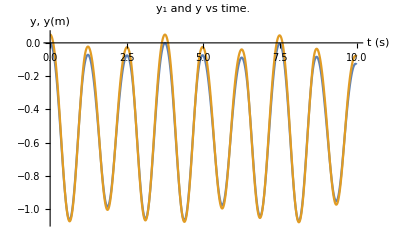

```mathematica
Plot[Evaluate[{Subscript[y, 1],Subscript[y, 2]}/.solndp],{t,0,10},PlotRange->All,AxesLabel->{"t (s)","y, y(m)"},PlotLabel->"y_1 and y vs time."]
```

Plot trajectories in x, y plane.

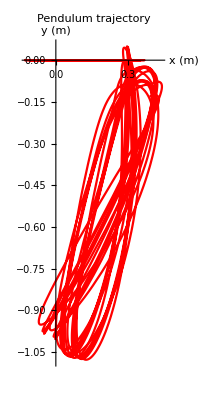

```mathematica
ParametricPlot[{{Subscript[x, 0],Subscript[y, 0]},{Subscript[x, 1],Subscript[y, 1]},{Subscript[x, 2],Subscript[y, 2]}}/.solndp,{t,0,10},PlotRange->All,AxesLabel->{"x (m)","y (m)"}, PlotLabel->"Pendulum trajectory", PlotStyle-> {Green, Blue, Red}]
```

Animate trajectories in x, y plane.

```mathematica
Animate[ParametricPlot[{{Subscript[x, 1],Subscript[y, 1]},{Subscript[x, 2],Subscript[y, 2]}}/.solndp,{t,0,tend},PlotRange->{{-1.5,1.5},{-2.5,0}},AxesLabel->{"x (m)","y (m)"},PlotLabel->"Pendulum trajectory"],{tend,0,10},AnimationRepetitions->3]
```

### Adding damping

We add terms proportional to each of the variables θ, ,  and  with the same proportionality constant .

Damped dynamical equations:

```mathematica
ELEθDamped=0==FullSimplify[D[dLdashdθ,t]-dLdθ +β θ'[t]]
```

0==0.882 Sin[θ[t]]+(1. β+(0.18-1.38778×10^-17 Cos[2 θ[t]]) s'[t]) θ'[t]+0.09 Cos[θ[t]] x''[t]+0.027 θ''[t]+s[t] (2.94 Sin[θ[t]]+0.6 s'[t] θ'[t]+0.3 Cos[θ[t]] x''[t]+(0.18+0.3 s[t]) θ''[t])

```mathematica
ELEαDamped=0==FullSimplify[D[dLdashdα,t]-dLdα +β α'[t]]
```

0==0.45 δ s[t] α[t]^2+β α'[t]+0.00025 α''[t]

```mathematica
ELEsDamped=0==FullSimplify[D[dLdashds,t]-dLds +β s'[t]]
```

0==-2.94 Cos[θ[t]]+0.15 δ α[t]^3+1. β s'[t]-0.09 θ'[t]^2+s[t] (10.-0.3 θ'[t]^2)+0.3 s''[t]+0.3 Sin[θ[t]] x''[t]

```mathematica
ELExDamped=0==FullSimplify[D[dLdashdx,t]-dLdx +β x'[t]]
```

0==β x'[t]+0.6 Cos[θ[t]] s'[t] θ'[t]-0.3 (0.3+s[t]) Sin[θ[t]] θ'[t]^2+0.3 Sin[θ[t]] s''[t]+0.602 x''[t]+0.3 Cos[θ[t]] (0.3+s[t]) θ''[t]

Choose the damping parameter and solve the Euler-Lagrange equation:

```mathematica
β=0.01; soln=NDSolve[{ELEθDamped,ELEαDamped,ELEsDamped,ELExDamped,θ[0]==Pi/2,α[0]==0,θ'[0]==0,α'[0]==0, s[0] == 0, s'[0] == 0, x[0] == 0, x'[0] == 0},{θ,α, s, x},{t,0,10}]
```

{{θ→InterpolatingFunction[…],α→InterpolatingFunction[…],s→InterpolatingFunction[…],x→InterpolatingFunction[…]}}

Plot y_1 and y_2 coordinates vs time. Include a title for the plot and axes labels with units.

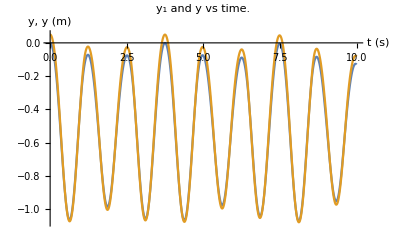

```mathematica
Plot[Evaluate[{Subscript[y, 1],Subscript[y, 2]}/.solndp],{t,0,10},PlotRange->All,AxesLabel->{"t (s)","y, y (m)"},PlotLabel->"y_1 and y vs time."]
```

```mathematica
Clear["Global`*"]
```

```mathematica
Clear[β]
```